```mathematica
(*2зад. Като използвате явния и неявния метод на Ойлер, решете моделното уравнение
du/dx=-10u, 0<x≤1
u(0)=1
при n=100, 1000,10000.  Начертайте графиките на абсолютните грешки по модул и ги сравнете.*)
(*explicit*)
```

```mathematica
explicitEuler[n_,f_]:= (
h=1.0/n;(*compute numerically*)
xList=Table[i*h,{i,0,n}];
yList=Table[0,{n+1}];

yList[[1]] = 1;
For[i=1, i<n+1, i++,
yList[[i+1]] = yList[[i]]+h*f[xList[[i]],yList[[i]]]
];

Transpose[{xList,yList}]
)
```

```mathematica
f[x_,u_]:=-10*u
exact[t_]=DSolve[{u'[t]==f[t,u[t]],u[0]==1},u[t],t][[1,1,2]];
(*exact[x_]:=E^(-10x);*)
plotExact = Plot[exact[x],{x,0, 1}, PlotStyle->Red, PlotRange->All];
n=100;
appr = explicitEuler[n,f];
```

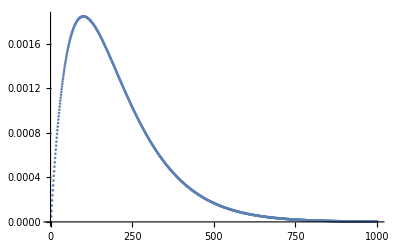

```mathematica
absErr = Abs[exact[xList] - appr[[All,2]]];
plot100= ListPlot[absErr]
```

```mathematica
n=1000;
appr = explicitEuler[n,f];
absErr = Abs[exact[xList] - appr[[All,2]]];
plot1000= ListPlot[absErr]
```

-Graphics-

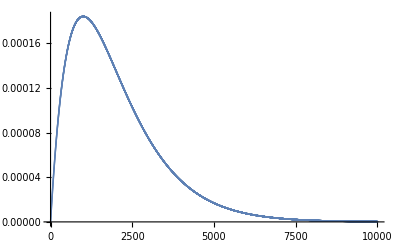

```mathematica
n=10000;
appr = explicitEuler[n,f];
absErr = Abs[exact[xList] - appr[[All,2]]];
plot10000= ListPlot[absErr]
```

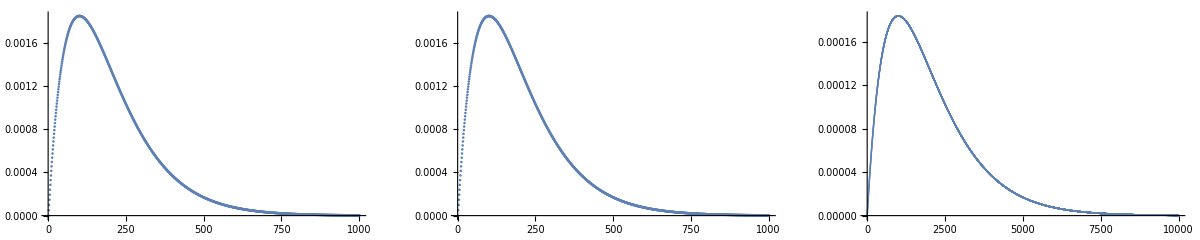

```mathematica
GraphicsRow[{plot100,plot1000,plot10000}]
```

```mathematica
(*implicit*)
implicitEuler[n_,f_]:= (
h=1.0/n;
xList=Table[i*h,{i,0,n}];
yList=Table[0,{n+1}];

yList[[1]] =1;
For[i=1, i<n+1, i++,
initialGuess =yList[[i]]+h*f[xList[[i]],yList[[i]]];
yList[[i+1]]=FindRoot[yNew==  yList[[i]]+h*f[xList[[i+1]],yNew],{yNew,initialGuess}][[1,2]]
];

Transpose[{xList,yList}]
)
```

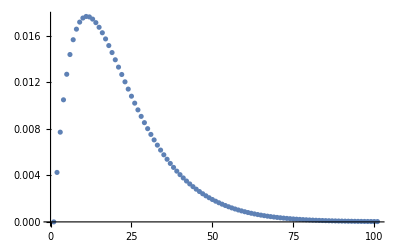

```mathematica
n=100;
appr = implicitEuler[n,f];
absErr = Abs[exact[xList] - appr[[All,2]]];
implPlot100= ListPlot[absErr]
```

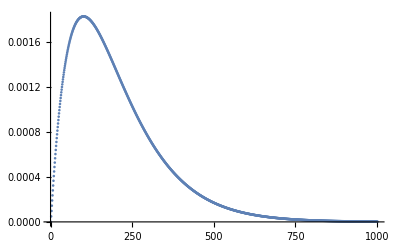

```mathematica
n=1000;
appr = implicitEuler[n,f];
absErr = Abs[exact[xList] - appr[[All,2]]];
implPlot1000= ListPlot[absErr]
```

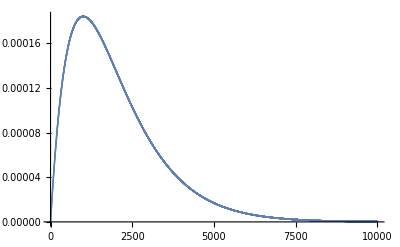

```mathematica
n=10000;
appr = implicitEuler[n,f];
absErr = Abs[exact[xList] - appr[[All,2]]];
implPlot10000= ListPlot[absErr]
```

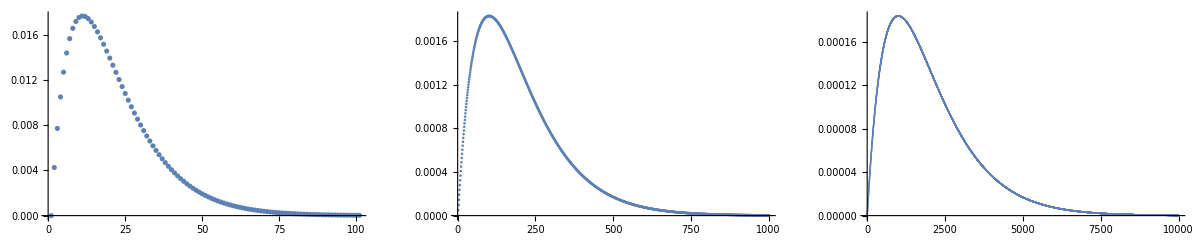

```mathematica
GraphicsRow[{implPlot100,implPlot1000,implPlot10000}]
```

```mathematica
(*3 зад. Пресметнете локалната грешка на апроксимация на диференчните схеми
(а) (Subscript[y, i+1]-Subscript[y, i])/h=1/(3h)(Subscript[y, i]-Subscript[y, i-1])+2/3 Subscript[f, i]
(b)Subscript[y, i+1]=Subscript[y, i]+h/2(3 Subscript[f, i]-Subscript[f, i-1])*)
```

```mathematica
(* 4 зад. Да се реши задачата на Коши 
du/dt=10u(1-u), 0<t≤6
u(0)=0.1
с явния и неявния метод на Ойлер за n=10,20, 35, 75, 500. Да се изобразят резултатите. *)
```

```mathematica
explicitEuler[n_,f_, t0_,T_,u0_]:= (
h=(T-t0)/n;(*compute numerically*)
xList=Table[t0 + i*h,{i,0,n}];
yList=Table[0,{n+1}];

yList[[1]] = u0;
For[i=1, i<n+1, i++,
yList[[i+1]] = yList[[i]]+h*f[xList[[i]],yList[[i]]]
];

Transpose[{xList,yList}]
)
```

```mathematica
f[x_,u_]:=10*u*(1-u)
exact[t_]=DSolve[{u'[x]==f[x,u[x]],u[0]==1/10},u[x],x][[1,1,2]];
```

```mathematica
n = {10,20,35,75,500};
plots = Table[0, {i,1,Length[n]}];
For[j=1, j≤Length[n],j++,
appr = explicitEuler[n[[j]],f,0,6,0.1];
plots[[j]] = Show[Plot[exact[x],{x,0,6}, PlotStyle-> Red, PlotRange->All],ListLinePlot[appr, PlotRange -> All]]
];
```

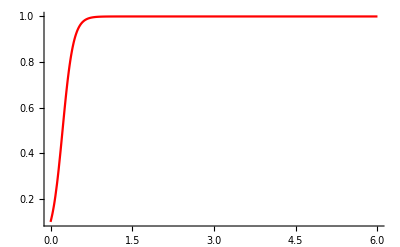
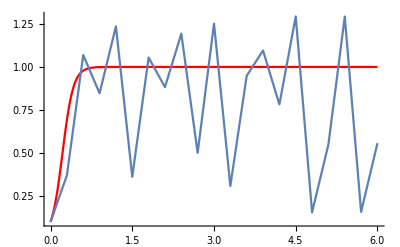
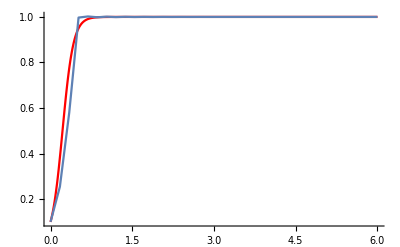
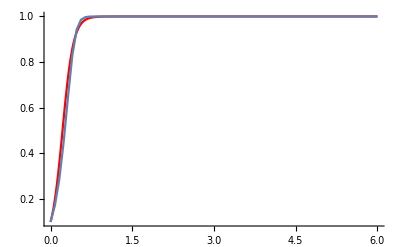
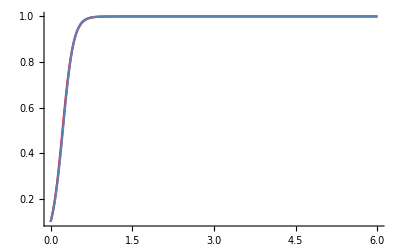

```mathematica
plots
```

```mathematica
implicitEuler[n_,f_,t0_,T_,u0_]:= (
h=(T-t0)/n;
xList=Table[t0 + i*h,{i,0,n}];
yList=Table[0,{n+1}];

yList[[1]] =u0;
For[i=1, i<n+1, i++,
initialGuess =yList[[i]]+h*f[xList[[i]],yList[[i]]];
yList[[i+1]]=FindRoot[yNew==  yList[[i]]+h*f[xList[[i+1]],yNew],{yNew,initialGuess}][[1,2]]
];

Transpose[{xList,yList}]
)
```

```mathematica
n = {10,20,35,75,500};
plots = Table[0, {i,1,Length[n]}];
For[j=1, j≤Length[n],j++,
appr = implicitEuler[n[[j]],f,0,6,0.1];
plots[[j]] = Show[Plot[exact[x],{x,0,6}, PlotStyle-> Red, PlotRange->All],ListLinePlot[appr, PlotRange -> All]]
];
```

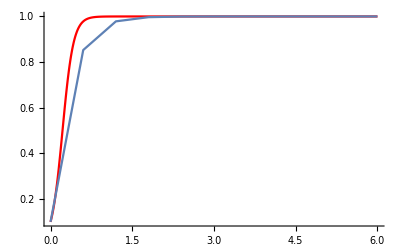
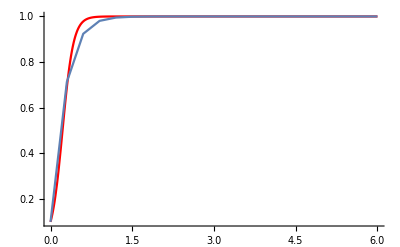
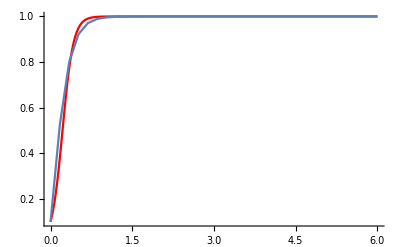
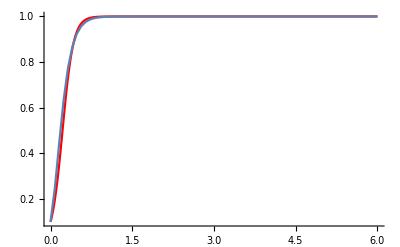
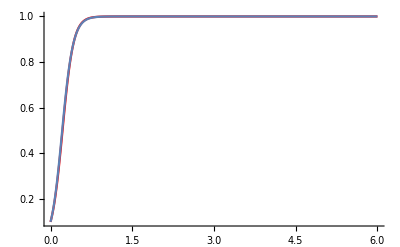

```mathematica
plots
```

```mathematica
(*du/dt = f(u) -avtonomno u-e (nqma t otdqsno). Kazvame, che E e ravnovesna tochka za u-eto, ako F(E) = 0.

5 зад. Да се изобразят точните решения на задачата на Коши 
du/dt=u(u-2), 0<t≤6
u(0)=а
при a=-0.5,0, 1, 2, 2.5. 
----------------------------
togava u(u-2) = 0 => u=0 ili u=2 *)
```

```mathematica
exact2[t_, a_] =DSolve[{u'[t] == u[t]*(u[t] - 2), u[0] == a},u[t],t][[1,1,2]];
```

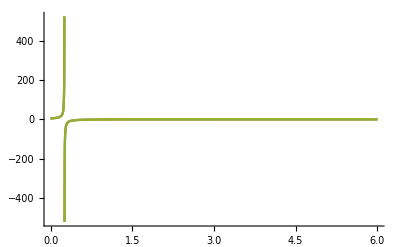

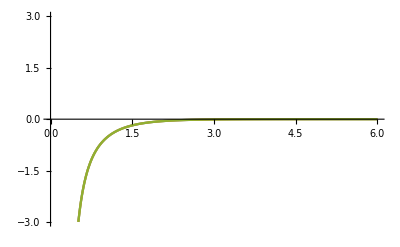

```mathematica
Plot[{exact2[t,-0.5],exact2[t,0],exact2[t,1]},{t,0,6}, PlotRange->All]
Plot[{exact2[t,1.999999],exact2[t,2],exact2[t,2.1]},{t,0,6},PlotRange->{{0,6},{-3,3}}]
```